```mathematica
ClearAll["Global`*"]
```

```mathematica
eq1=1+B1==C1+D1;
eq2=I k (1-B1)==λ (C1-D1);
eq3=C1 Exp[λ L]+D1 Exp[-λ L]==F1 Exp[I k L];
eq4=λ (C1 Exp[λ L]-D1 Exp[-λ L])==I k F1 Exp[I k L];


(*Solve the equations*)
solution=Solve[{eq1,eq2,eq3,eq4},{B1,C1,D1,F1}]
```

{{B1→-(((-1+ⅇ^(2 L λ)) (k^2+λ^2))/(k^2-ⅇ^(2 L λ) k^2-2 ⅈ k λ-2 ⅈ ⅇ^(2 L λ) k λ-λ^2+ⅇ^(2 L λ) λ^2)),C1→-((2 k (k-ⅈ λ))/(-k^2+ⅇ^(2 L λ) k^2+2 ⅈ k λ+2 ⅈ ⅇ^(2 L λ) k λ+λ^2-ⅇ^(2 L λ) λ^2)),D1→(2 ⅇ^(2 L λ) k (k+ⅈ λ))/(-k^2+ⅇ^(2 L λ) k^2+2 ⅈ k λ+2 ⅈ ⅇ^(2 L λ) k λ+λ^2-ⅇ^(2 L λ) λ^2),F1→-((4 ⅇ^(-ⅈ k L+L λ) k λ)/(-ⅈ k^2+ⅈ ⅇ^(2 L λ) k^2-2 k λ-2 ⅇ^(2 L λ) k λ+ⅈ λ^2-ⅈ ⅇ^(2 L λ) λ^2))}}

```mathematica
-((4 ⅇ^(-ⅈ k L+L λ) k λ)/(-ⅈ k^2+ⅈ ⅇ^(2 L λ) k^2-2 k λ-2 ⅇ^(2 L λ) k λ+ⅈ λ^2-ⅈ ⅇ^(2 L λ) λ^2))//FullSimplify
```

(2 ⅈ ⅇ^(-ⅈ k L) k λ)/(2 ⅈ k λ Cosh[L λ]+(k-λ) (k+λ) Sinh[L λ])

```mathematica
1/(Cosh[L lambda]^2+((k^2-lambda^2)^2 Sinh[L lambda]^2)/(4 k^2 lambda^2))/.k-> √(((2M)/ℏ^2)(En))/.lambda-> √(((2M)/ℏ^2)(U-En))
```

```mathematica
1/(Cosh[√2 L √((M (-En+U))/ℏ^2)]^2+(((2 En M)/ℏ^2-(2 M (-En+U))/ℏ^2)^2 ℏ^4 Sinh[√2 L √((M (-En+U))/ℏ^2)]^2)/(16 En M^2 (-En+U)))//FullSimplify
```

(8 En (En-U))/(8 En^2-8 En U+U^2-U^2 Cosh[2 √2 L √((M (-En+U))/ℏ^2)])

```mathematica
(*Minimum constant*)kMin=0.1;(*Maximum value*)kMax=5;(*Step for k*)(*Define the reflection and transmission functions*)R:=
R:=1/(1+(4 En (-En+U) Csch[L √(-En+U)]^2)/U^2)
T:=1/(Cosh[L √(-En+U)]^2+((2 En-U)^2 Sinh[L √(-En+U)]^2)/(4 En (-En+U)))

(*Plot Reflection and Transmission curves*)
Plot[{R/.En->kMin/.L->1,T/.En->kMin/.L->1},{U,kMin,kMax},PlotLabels->{"Reflection (R)","Transmission (T)"},PlotStyle->{Red,Blue},AxesLabel->{"U","R, T"},PlotRange->{0,1},GridLines->Automatic]
```

-Graphics-

```mathematica
(*Plot Reflection and Transmission curves*)
Plot[{R/.U->2/.En->1,T/.U->2/.En->1},{L,0.1,5},PlotLabels->{"Reflection (R)","Transmission (T)"},PlotStyle->{Red,Blue},AxesLabel->{"L","R, T"},PlotRange->{0,1},GridLines->Automatic]
```

-Graphics-

```mathematica
(*Plot Reflection and Transmission curves*)
Plot[{R/.U->2/.L->1,T/.U->2/.L->1},{En,0.1,2},PlotLabels->{"Reflection (R)","Transmission (T)"},PlotStyle->{Red,Blue},AxesLabel->{"E","R, T"},PlotRange->{0,1},GridLines->Automatic]
```

-Graphics-

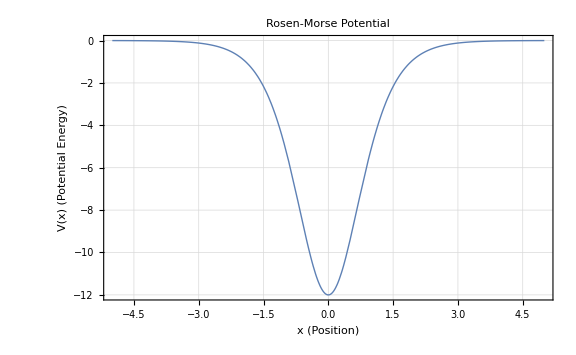

```mathematica
Plot[-12 Sech[x]^2,{x,-5,5},PlotRange->All,PlotStyle->Thick,AxesLabel->{"x","V(x)"},PlotLabel->"Symmetric Rosen-Morse Potential",LabelStyle->{FontSize->14,Bold},TicksStyle->Directive[Black,Bold],GridLines->Automatic,Frame->True,FrameLabel->{"x (Position)","V(x) (Potential Energy)"},FrameStyle->Directive[Gray,Bold],ImageSize->Large]
```

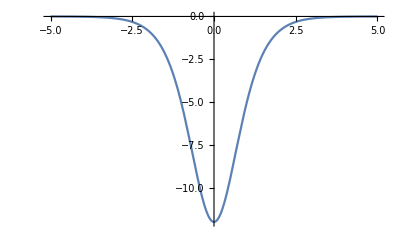

```mathematica
Plot[-12 Sech[x]^2,{x,-5,5}]
```

```mathematica
Integrate[Sech[x]^6,{x,-∞,∞}]
```

16/15

```mathematica
Integrate[Sech[x]^4 Tanh[x]^2,{x,-∞,∞}]
```

4/15

```mathematica
Integrate[Sech[x]^2(5 Tanh[x]^2-1)^2,{x,-∞,∞}]
```

16/3